```mathematica
Sinh[0]
```

0

```mathematica
B=1
```

1

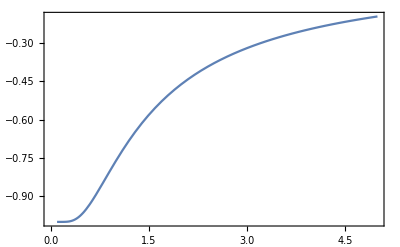

```mathematica
Plot[- Tanh[1/x],{x,0.1,5},AxesOrigin->{0,-1},Frame->True]
```

```mathematica
Cosh[0]
```

1

```mathematica
Clear[B]
```

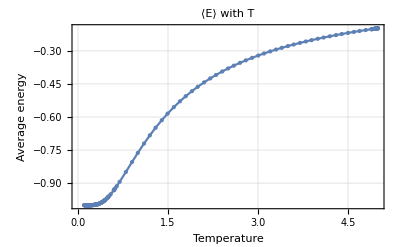

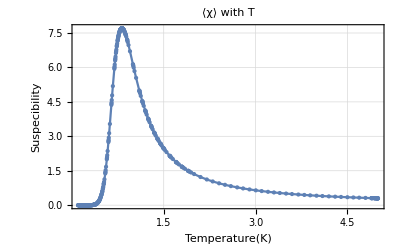

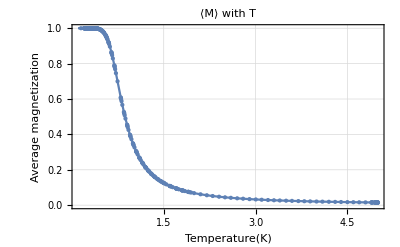

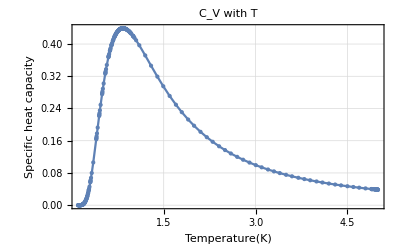

```mathematica
B=0.05;J=1;
Plot[-J Tanh[J/x],{x,0.1,5},AxesOrigin->{0,-1},Frame->True,PlotLabel->"⟨Ε⟩ with T",FrameLabel->{"Temperature","Average energy"},Mesh->All,GridLines->Automatic,FrameTicks->None]
Plot[(Exp[-4 J/T] Cosh[B/T])/(T (Sinh[B/T]^2+Exp[-4  J/T])^(3/2)),{T,0.1,5},Frame->True,PlotLabel->"⟨χ⟩ with T",FrameLabel->{"Temperature(K)","Suspecibility"},Mesh->All,GridLines->Automatic(*,FrameTicks->None*)]
Plot[Sinh[B/T]/(√(Sinh[B/T]^2+Exp[-4 J/T])),{T,0.1,5},Frame->True,PlotLabel->"⟨Μ⟩ with T",FrameLabel->{"Temperature(K)","Average magnetization"},Mesh->All,GridLines->Automatic,FrameTicks->None]
Plot[(J^2 Sech[J/T]^2)/T^2,{T,0.1,5},Frame->True,PlotLabel->"C_V with T",FrameLabel->{"Temperature(K)","Specific heat capacity"},Mesh->All,GridLines->Automatic(*,FrameTicks->None*)]
```

```mathematica
Tanh[-1]//N
```

-0.761594